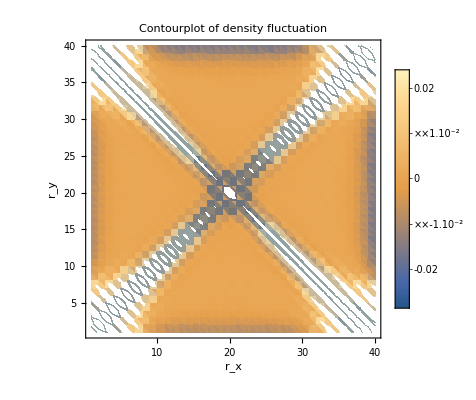

-Graphics3D-

rhoplot.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
(****************************************)
Clear[data,datac,rx,ry,rho];
data=Import["result.dat","Table"];
rx=data[[;;,1]];
ry=data[[;;,2]];
rho=data[[;;,3]]/1000;
datac=Transpose[{rx,ry,rho}];
rhoplot=ListDensityPlot[datac,Axes->True,InterpolationOrder->6,FrameLabel->{"r_x","r_y"},PlotLabel->"Contourplot of density fluctuation",PlotLegends->Automatic]
(*******************)
ListContourPlot[datac,Axes->True,InterpolationOrder->3,FrameLabel->{"r_x","r_y"},PlotLabel->"Contourplot of density fluctuation",ColorFunction->"Pastel",PlotLegends->Automatic];
ListPlot3D[{datac},PlotStyle->Directive[Orange,Specularity[White,20]]]
Export["rhoplot.jpg",rhoplot]
```

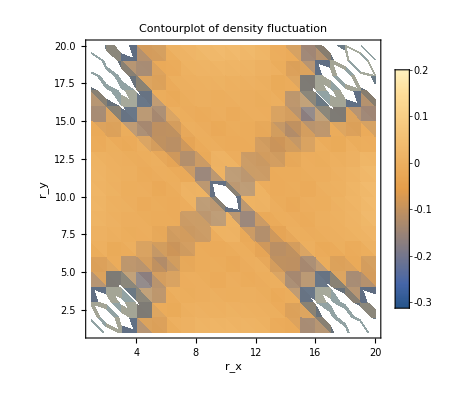

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
(****************************************)
Clear[data,datac,rx,ry,rho,n];
data=Import["result0.dat","Table"];
rx=data[[;;,1]];
ry=data[[;;,2]];
rho=data[[;;,3]]/100;
n=Sqrt[Length[rx]];(*lattice size*)
datac=Transpose[{rx,ry,rho}];
rhoplot=ListDensityPlot[datac,Axes->True,InterpolationOrder->3,FrameLabel->{"r_x","r_y"},PlotLabel->"Contourplot of density fluctuation",PlotLegends->Automatic]
(*******************)
ListContourPlot[datac,Axes->True,InterpolationOrder->3,FrameLabel->{"r_x","r_y"},PlotLabel->{"Contourplot of density fluctuation"},ColorFunction->"Pastel",PlotLegends->Automatic];
ListPointPlot3D[{datac},ColorFunction->"Rainbow",Filling->Bottom]
ListPointPlot3D[{datac},ColorFunction->"Rainbow"]
ListPlot3D[{datac},ColorFunction->"Rainbow"]
(*Export["rhoplot.jpg",chiplot]*)
```